```mathematica
Needs["Notation`"];
Notation[Δ ⟺ cd]
Notation[𝒿 ⟺ cj]
```

```mathematica
<<sneg`sneg`;
snegfermionoperators[a,b,c];
snegrealconstants[cj,U,U1,t,t22,t23,cd,x];
```

sneg 1.250 Copyright (C) 2016 Rok Zitko

```mathematica
myop = {a[1],a[2],a[3],a[4],a[5],a[6]}
```

{a^,a[2],a[3],a[4],a[5],a[6]}

```mathematica
makebasis[myop]
```

{a_(1⇑)^†,a_(1↓)^†,a_(2⇑)^†,a_(2↓)^†,a_(3⇑)^†,a_(3↓)^†,a_(4⇑)^†,a_(4↓)^†,a_(5⇑)^†,a_(5↓)^†,a_(6⇑)^†,a_(6↓)^†}

```mathematica
vc6= qszbasisvc[myop];
```

```mathematica
basise4p2 = Select[vc6,#[[1]]=={-2,2}&][[1,2]];
```

```mathematica
basise4p1 = Select[vc6,#[[1]]=={-2,1}&][[1,2]];
```

```mathematica
basise40 = Select[vc6,#[[1]]=={-2,0}&][[1,2]];
```

```mathematica
basise4n1 = Select[vc6,#[[1]]=={-2,-1}&][[1,2]];
```

```mathematica
basise4n2= Select[vc6,#[[1]]=={-2,-2}&][[1,2]];
```

```mathematica
hhop = -t22(hop[a[2],a[5]])- t22(hop[a[3],a[6]])-t22(hop[a[1],a[4]])-t23(hop[a[2],a[6]]+hop[a[3],a[5]])
```

-t22 (a_(1↓)^†·a_(4↓)^+a_(1⇑)^†·a_(4⇑)^+a_(4↓)^†·a_(1↓)^+a_(4⇑)^†·a_(1⇑)^)-t22 (a_(2↓)^†·a_(5↓)^+a_(2⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(2↓)^+a_(5⇑)^†·a_(2⇑)^)-t23 (a_(2↓)^†·a_(6↓)^+a_(2⇑)^†·a_(6⇑)^+a_(3↓)^†·a_(5↓)^+a_(3⇑)^†·a_(5⇑)^+a_(5↓)^†·a_(3↓)^+a_(5⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(2↓)^+a_(6⇑)^†·a_(2⇑)^)-t22 (a_(3↓)^†·a_(6↓)^+a_(3⇑)^†·a_(6⇑)^+a_(6↓)^†·a_(3↓)^+a_(6⇑)^†·a_(3⇑)^)

```mathematica
hhd = cd(number[a[3]]+number[a[6]])(* 0.0(number[a[1]]+number[a[2]]+number[a[4]]+number[a[5]])*)
```

Δ (a_(3↓)^†·a_(3↓)^+a_(3⇑)^†·a_(3⇑)^+a_(6↓)^†·a_(6↓)^+a_(6⇑)^†·a_(6⇑)^)

```mathematica
hhj = (U-3cj)(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])
```

(-3 𝒿+U) (-(a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^)-a_(1↓)^†·a_(3↓)^†·a_(1↓)^·a_(3↓)^-a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-a_(1⇑)^†·a_(3⇑)^†·a_(1⇑)^·a_(3⇑)^-a_(2↓)^†·a_(3↓)^†·a_(2↓)^·a_(3↓)^-a_(2⇑)^†·a_(3⇑)^†·a_(2⇑)^·a_(3⇑)^-a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^-a_(4↓)^†·a_(6↓)^†·a_(4↓)^·a_(6↓)^-a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^-a_(4⇑)^†·a_(6⇑)^†·a_(4⇑)^·a_(6⇑)^-a_(5↓)^†·a_(6↓)^†·a_(5↓)^·a_(6↓)^-a_(5⇑)^†·a_(6⇑)^†·a_(5⇑)^·a_(6⇑)^)

```mathematica
hhu = U(hubbard[a[1]]+hubbard[a[2]]+hubbard[a[3]]+hubbard[a[4]]+hubbard[a[5]]+hubbard[a[6]])
```

U (-(a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(6↓)^·a_(6⇑)^)

```mathematica
hhu1 = (*U1(nc[number[a[1],UP],number[a[2],UP]]+nc[number[a[1],UP],number[a[3],UP]]+nc[number[a[2],UP],number[a[3],UP]]+nc[number[a[1],DO],number[a[2],DO]]+nc[number[a[1],DO],number[a[3],DO]]+nc[number[a[2],DO],number[a[3],DO]]+nc[number[a[4],UP],number[a[5],UP]]+nc[number[a[4],UP],number[a[6],UP]]+nc[number[a[5],UP],number[a[6],UP]]+nc[number[a[4],DO],number[a[5],DO]]+nc[number[a[4],DO],number[a[6],DO]]+nc[number[a[5],DO],number[a[6],DO]])+*)(U-2cj)(nc[number[a[1],UP],number[a[2],DO]]+nc[number[a[1],UP],number[a[3],DO]]+nc[number[a[2],UP],number[a[3],DO]]+nc[number[a[1],DO],number[a[2],UP]]+nc[number[a[1],DO],number[a[3],UP]]+nc[number[a[2],DO],number[a[3],UP]]+nc[number[a[4],UP],number[a[5],DO]]+nc[number[a[4],UP],number[a[6],DO]]+nc[number[a[5],UP],number[a[6],DO]]+nc[number[a[4],DO],number[a[5],UP]]+nc[number[a[4],DO],number[a[6],UP]]+nc[number[a[5],DO],number[a[6],UP]])//Simplify
```

(2 𝒿-U) (a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^+a_(1↓)^†·a_(3⇑)^†·a_(1↓)^·a_(3⇑)^+a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^+a_(1⇑)^†·a_(3↓)^†·a_(1⇑)^·a_(3↓)^+a_(2↓)^†·a_(3⇑)^†·a_(2↓)^·a_(3⇑)^+a_(2⇑)^†·a_(3↓)^†·a_(2⇑)^·a_(3↓)^+a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^+a_(4↓)^†·a_(6⇑)^†·a_(4↓)^·a_(6⇑)^+a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^+a_(4⇑)^†·a_(6↓)^†·a_(4⇑)^·a_(6↓)^+a_(5↓)^†·a_(6⇑)^†·a_(5↓)^·a_(6⇑)^+a_(5⇑)^†·a_(6↓)^†·a_(5⇑)^·a_(6↓)^)

```mathematica
(* U' = U -2J, since Hamiltonian maintains rotation invariance*)
```

```mathematica
(* pair fliping, hhpf*)
```

```mathematica
hhpf1=nc[a[CR,1,UP],a[AN,1,DO],a[CR,2,DO],a[AN,2,UP]]+nc[a[CR,1,UP],a[AN,1,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,2,UP],a[AN,2,DO],a[CR,3,DO],a[AN,3,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,5,DO],a[AN,5,UP]]+nc[a[CR,4,UP],a[AN,4,DO],a[CR,6,DO],a[AN,6,UP]]+nc[a[CR,5,UP],a[AN,5,DO],a[CR,6,DO],a[AN,6,UP]]
```

-(a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^)-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^

```mathematica
hhpf2=conj[hhpf1]
```

-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^

```mathematica
hhpf=-cj (hhpf1+hhpf2)
```

-𝒿 (-(a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^)-a_(1↓)^†·a_(3⇑)^†·a_(1⇑)^·a_(3↓)^-a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^-a_(1⇑)^†·a_(3↓)^†·a_(1↓)^·a_(3⇑)^-a_(2↓)^†·a_(3⇑)^†·a_(2⇑)^·a_(3↓)^-a_(2⇑)^†·a_(3↓)^†·a_(2↓)^·a_(3⇑)^-a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-a_(4↓)^†·a_(6⇑)^†·a_(4⇑)^·a_(6↓)^-a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^-a_(4⇑)^†·a_(6↓)^†·a_(4↓)^·a_(6⇑)^-a_(5↓)^†·a_(6⇑)^†·a_(5⇑)^·a_(6↓)^-a_(5⇑)^†·a_(6↓)^†·a_(5↓)^·a_(6⇑)^)

```mathematica
(*pair hopping, hhph*)
```

```mathematica
hhph1=nc[a[CR,1,UP],a[AN,2,UP],a[CR,1,DO],a[AN,2,DO]]+nc[a[CR,1,UP],a[AN,3,UP],a[CR,1,DO],a[AN,3,DO]]+nc[a[CR,2,UP],a[AN,3,UP],a[CR,2,DO],a[AN,3,DO]]+nc[a[CR,4,UP],a[AN,5,UP],a[CR,4,DO],a[AN,5,DO]]+nc[a[CR,4,UP],a[AN,6,UP],a[CR,4,DO],a[AN,6,DO]]+nc[a[CR,5,UP],a[AN,6,UP],a[CR,5,DO],a[AN,6,DO]]
```

-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^

```mathematica
hhph2=conj[hhph1]
```

-(a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^)-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^

```mathematica
hhph=-cj (hhph1+hhph2)
```

-𝒿 (-(a_(1↓)^†·a_(1⇑)^†·a_(2↓)^·a_(2⇑)^)-a_(1↓)^†·a_(1⇑)^†·a_(3↓)^·a_(3⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(1↓)^·a_(1⇑)^-a_(2↓)^†·a_(2⇑)^†·a_(3↓)^·a_(3⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(1↓)^·a_(1⇑)^-a_(3↓)^†·a_(3⇑)^†·a_(2↓)^·a_(2⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(5↓)^·a_(5⇑)^-a_(4↓)^†·a_(4⇑)^†·a_(6↓)^·a_(6⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(4↓)^·a_(4⇑)^-a_(5↓)^†·a_(5⇑)^†·a_(6↓)^·a_(6⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(4↓)^·a_(4⇑)^-a_(6↓)^†·a_(6⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
ham = hhop + hhu + hhj +hhu1+hhd+hhpf+hhph//Simplify
(*ham= hhop + hhu + hhj +hhu1+hhd*)
```

```mathematica
-t22 (Subscript[a, 1"↓"]^("†")·Subscript[a, 4"↓"]^("")+Subscript[a, 1"⇑"]^("†")·Subscript[a, 4"⇑"]^("")+Subscript[a, 4"↓"]^("†")·Subscript[a, 1"↓"]^("")+Subscript[a, 4"⇑"]^("†")·Subscript[a, 1"⇑"]^(""))-t22 (Subscript[a, 2"↓"]^("†")·Subscript[a, 5"↓"]^("")+Subscript[a, 2"⇑"]^("†")·Subscript[a, 5"⇑"]^("")+Subscript[a, 5"↓"]^("†")·Subscript[a, 2"↓"]^("")+Subscript[a, 5"⇑"]^("†")·Subscript[a, 2"⇑"]^(""))-t23 (Subscript[a, 2"↓"]^("†")·Subscript[a, 6"↓"]^("")+Subscript[a, 2"⇑"]^("†")·Subscript[a, 6"⇑"]^("")+Subscript[a, 3"↓"]^("†")·Subscript[a, 5"↓"]^("")+Subscript[a, 3"⇑"]^("†")·Subscript[a, 5"⇑"]^("")+Subscript[a, 5"↓"]^("†")·Subscript[a, 3"↓"]^("")+Subscript[a, 5"⇑"]^("†")·Subscript[a, 3"⇑"]^("")+Subscript[a, 6"↓"]^("†")·Subscript[a, 2"↓"]^("")+Subscript[a, 6"⇑"]^("†")·Subscript[a, 2"⇑"]^(""))-t22 (Subscript[a, 3"↓"]^("†")·Subscript[a, 6"↓"]^("")+Subscript[a, 3"⇑"]^("†")·Subscript[a, 6"⇑"]^("")+Subscript[a, 6"↓"]^("†")·Subscript[a, 3"↓"]^("")+Subscript[a, 6"⇑"]^("†")·Subscript[a, 3"⇑"]^(""))+Δ (Subscript[a, 3"↓"]^("†")·Subscript[a, 3"↓"]^("")+Subscript[a, 3"⇑"]^("†")·Subscript[a, 3"⇑"]^("")+Subscript[a, 6"↓"]^("†")·Subscript[a, 6"↓"]^("")+Subscript[a, 6"⇑"]^("†")·Subscript[a, 6"⇑"]^(""))+𝒿 (Subscript[a, 1"↓"]^("†")·Subscript[a, 2"⇑"]^("†")·Subscript[a, 1"⇑"]^("")·Subscript[a, 2"↓"]^("")+Subscript[a, 1"↓"]^("†")·Subscript[a, 3"⇑"]^("†")·Subscript[a, 1"⇑"]^("")·Subscript[a, 3"↓"]^("")+Subscript[a, 1"⇑"]^("†")·Subscript[a, 2"↓"]^("†")·Subscript[a, 1"↓"]^("")·Subscript[a, 2"⇑"]^("")+Subscript[a, 1"⇑"]^("†")·Subscript[a, 3"↓"]^("†")·Subscript[a, 1"↓"]^("")·Subscript[a, 3"⇑"]^("")+Subscript[a, 2"↓"]^("†")·Subscript[a, 3"⇑"]^("†")·Subscript[a, 2"⇑"]^("")·Subscript[a, 3"↓"]^("")+Subscript[a, 2"⇑"]^("†")·Subscript[a, 3"↓"]^("†")·Subscript[a, 2"↓"]^("")·Subscript[a, 3"⇑"]^("")+Subscript[a, 4"↓"]^("†")·Subscript[a, 5"⇑"]^("†")·Subscript[a, 4"⇑"]^("")·Subscript[a, 5"↓"]^("")+Subscript[a, 4"↓"]^("†")·Subscript[a, 6"⇑"]^("†")·Subscript[a, 4"⇑"]^("")·Subscript[a, 6"↓"]^("")+Subscript[a, 4"⇑"]^("†")·Subscript[a, 5"↓"]^("†")·Subscript[a, 4"↓"]^("")·Subscript[a, 5"⇑"]^("")+Subscript[a, 4"⇑"]^("†")·Subscript[a, 6"↓"]^("†")·Subscript[a, 4"↓"]^("")·Subscript[a, 6"⇑"]^("")+Subscript[a, 5"↓"]^("†")·Subscript[a, 6"⇑"]^("†")·Subscript[a, 5"⇑"]^("")·Subscript[a, 6"↓"]^("")+Subscript[a, 5"⇑"]^("†")·Subscript[a, 6"↓"]^("†")·Subscript[a, 5"↓"]^("")·Subscript[a, 6"⇑"]^(""))+(2 𝒿-U) (Subscript[a, 1"↓"]^("†")·Subscript[a, 2"⇑"]^("†")·Subscript[a, 1"↓"]^("")·Subscript[a, 2"⇑"]^("")+Subscript[a, 1"↓"]^("†")·Subscript[a, 3"⇑"]^("†")·Subscript[a, 1"↓"]^("")·Subscript[a, 3"⇑"]^("")+Subscript[a, 1"⇑"]^("†")·Subscript[a, 2"↓"]^("†")·Subscript[a, 1"⇑"]^("")·Subscript[a, 2"↓"]^("")+Subscript[a, 1"⇑"]^("†")·Subscript[a, 3"↓"]^("†")·Subscript[a, 1"⇑"]^("")·Subscript[a, 3"↓"]^("")+Subscript[a, 2"↓"]^("†")·Subscript[a, 3"⇑"]^("†")·Subscript[a, 2"↓"]^("")·Subscript[a, 3"⇑"]^("")+Subscript[a, 2"⇑"]^("†")·Subscript[a, 3"↓"]^("†")·Subscript[a, 2"⇑"]^("")·Subscript[a, 3"↓"]^("")+Subscript[a, 4"↓"]^("†")·Subscript[a, 5"⇑"]^("†")·Subscript[a, 4"↓"]^("")·Subscript[a, 5"⇑"]^("")+Subscript[a, 4"↓"]^("†")·Subscript[a, 6"⇑"]^("†")·Subscript[a, 4"↓"]^("")·Subscript[a, 6"⇑"]^("")+Subscript[a, 4"⇑"]^("†")·Subscript[a, 5"↓"]^("†")·Subscript[a, 4"⇑"]^("")·Subscript[a, 5"↓"]^("")+Subscript[a, 4"⇑"]^("†")·Subscript[a, 6"↓"]^("†")·Subscript[a, 4"⇑"]^("")·Subscript[a, 6"↓"]^("")+Subscript[a, 5"↓"]^("†")·Subscript[a, 6"⇑"]^("†")·Subscript[a, 5"↓"]^("")·Subscript[a, 6"⇑"]^("")+Subscript[a, 5"⇑"]^("†")·Subscript[a, 6"↓"]^("†")·Subscript[a, 5"⇑"]^("")·Subscript[a, 6"↓"]^(""))+(3 𝒿-U) (Subscript[a, 1"↓"]^("†")·Subscript[a, 2"↓"]^("†")·Subscript[a, 1"↓"]^("")·Subscript[a, 2"↓"]^("")+Subscript[a, 1"↓"]^("†")·Subscript[a, 3"↓"]^("†")·Subscript[a, 1"↓"]^("")·Subscript[a, 3"↓"]^("")+Subscript[a, 1"⇑"]^("†")·Subscript[a, 2"⇑"]^("†")·Subscript[a, 1"⇑"]^("")·Subscript[a, 2"⇑"]^("")+Subscript[a, 1"⇑"]^("†")·Subscript[a, 3"⇑"]^("†")·Subscript[a, 1"⇑"]^("")·Subscript[a, 3"⇑"]^("")+Subscript[a, 2"↓"]^("†")·Subscript[a, 3"↓"]^("†")·Subscript[a, 2"↓"]^("")·Subscript[a, 3"↓"]^("")+Subscript[a, 2"⇑"]^("†")·Subscript[a, 3"⇑"]^("†")·Subscript[a, 2"⇑"]^("")·Subscript[a, 3"⇑"]^("")+Subscript[a, 4"↓"]^("†")·Subscript[a, 5"↓"]^("†")·Subscript[a, 4"↓"]^("")·Subscript[a, 5"↓"]^("")+Subscript[a, 4"↓"]^("†")·Subscript[a, 6"↓"]^("†")·Subscript[a, 4"↓"]^("")·Subscript[a, 6"↓"]^("")+Subscript[a, 4"⇑"]^("†")·Subscript[a, 5"⇑"]^("†")·Subscript[a, 4"⇑"]^("")·Subscript[a, 5"⇑"]^("")+Subscript[a, 4"⇑"]^("†")·Subscript[a, 6"⇑"]^("†")·Subscript[a, 4"⇑"]^("")·Subscript[a, 6"⇑"]^("")+Subscript[a, 5"↓"]^("†")·Subscript[a, 6"↓"]^("†")·Subscript[a, 5"↓"]^("")·Subscript[a, 6"↓"]^("")+Subscript[a, 5"⇑"]^("†")·Subscript[a, 6"⇑"]^("†")·Subscript[a, 5"⇑"]^("")·Subscript[a, 6"⇑"]^(""))+𝒿 (Subscript[a, 1"↓"]^("†")·Subscript[a, 1"⇑"]^("†")·Subscript[a, 2"↓"]^("")·Subscript[a, 2"⇑"]^("")+Subscript[a, 1"↓"]^("†")·Subscript[a, 1"⇑"]^("†")·Subscript[a, 3"↓"]^("")·Subscript[a, 3"⇑"]^("")+Subscript[a, 2"↓"]^("†")·Subscript[a, 2"⇑"]^("†")·Subscript[a, 1"↓"]^("")·Subscript[a, 1"⇑"]^("")+Subscript[a, 2"↓"]^("†")·Subscript[a, 2"⇑"]^("†")·Subscript[a, 3"↓"]^("")·Subscript[a, 3"⇑"]^("")+Subscript[a, 3"↓"]^("†")·Subscript[a, 3"⇑"]^("†")·Subscript[a, 1"↓"]^("")·Subscript[a, 1"⇑"]^("")+Subscript[a, 3"↓"]^("†")·Subscript[a, 3"⇑"]^("†")·Subscript[a, 2"↓"]^("")·Subscript[a, 2"⇑"]^("")+Subscript[a, 4"↓"]^("†")·Subscript[a, 4"⇑"]^("†")·Subscript[a, 5"↓"]^("")·Subscript[a, 5"⇑"]^("")+Subscript[a, 4"↓"]^("†")·Subscript[a, 4"⇑"]^("†")·Subscript[a, 6"↓"]^("")·Subscript[a, 6"⇑"]^("")+Subscript[a, 5"↓"]^("†")·Subscript[a, 5"⇑"]^("†")·Subscript[a, 4"↓"]^("")·Subscript[a, 4"⇑"]^("")+Subscript[a, 5"↓"]^("†")·Subscript[a, 5"⇑"]^("†")·Subscript[a, 6"↓"]^("")·Subscript[a, 6"⇑"]^("")+Subscript[a, 6"↓"]^("†")·Subscript[a, 6"⇑"]^("†")·Subscript[a, 4"↓"]^("")·Subscript[a, 4"⇑"]^("")+Subscript[a, 6"↓"]^("†")·Subscript[a, 6"⇑"]^("†")·Subscript[a, 5"↓"]^("")·Subscript[a, 5"⇑"]^(""))-U (Subscript[a, 1"↓"]^("†")·Subscript[a, 1"⇑"]^("†")·Subscript[a, 1"↓"]^("")·Subscript[a, 1"⇑"]^("")+Subscript[a, 2"↓"]^("†")·Subscript[a, 2"⇑"]^("†")·Subscript[a, 2"↓"]^("")·Subscript[a, 2"⇑"]^("")+Subscript[a, 3"↓"]^("†")·Subscript[a, 3"⇑"]^("†")·Subscript[a, 3"↓"]^("")·Subscript[a, 3"⇑"]^("")+Subscript[a, 4"↓"]^("†")·Subscript[a, 4"⇑"]^("†")·Subscript[a, 4"↓"]^("")·Subscript[a, 4"⇑"]^("")+Subscript[a, 5"↓"]^("†")·Subscript[a, 5"⇑"]^("†")·Subscript[a, 5"↓"]^("")·Subscript[a, 5"⇑"]^("")+Subscript[a, 6"↓"]^("†")·Subscript[a, 6"⇑"]^("†")·Subscript[a, 6"↓"]^("")·Subscript[a, 6"⇑"]^(""))
```

```mathematica
basise4n1;
```

```mathematica
basise40//Dimensions
basise4n1//Dimensions
basise4n2//Dimensions
basise4p2//Dimensions
basise4p1//Dimensions
```

{225}

{120}

{15}

{15}

{120}

```mathematica
mybasis={basise4n1,basise4n2,basise40,basise4p1,basise4p2}//Flatten;
```

```mathematica
td={cd->0.7,cj->U/5,U->4,t23->x t22,t22->0.3}
```

{Δ→0.7,𝒿→U/5,U→4,t23→t22 x,t22→0.3}

```mathematica
mymat=matrixrepresentationop[ham,mybasis]//.td;
```

```mathematica
vals1=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[1]]},{xx,0,4,0.2}];
vals2=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[2]]},{xx,0,4,0.2}];
vals3=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[3]]},{xx,0,4,0.2}];
vals4=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[4]]},{xx,0,4,0.2}];
vals5=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[5]]},{xx,0,4,0.2}];
vals6=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[6]]},{xx,0,4,0.2}];
vals7=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[7]]},{xx,0,4,0.2}];
vals8=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[8]]},{xx,0,4,0.2}];
vals9=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[9]]},{xx,0,4,0.2}];
vals10=Table[{xx,Sort[Eigenvalues[mymat/.x->xx]][[10]]},{xx,0,4,0.2}];
```

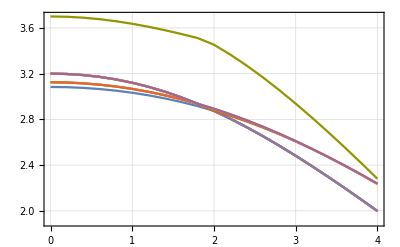

```mathematica
ListLinePlot[{vals1,vals2,vals3,vals4,vals5,vals6,vals7,vals8,vals9,vals10},Frame->True,GridLines->Automatic]
```

```mathematica
(** now we calculate the expection value of the square of spin <|S^2|>, S= s1+s2+s4+s5*)
```

```mathematica
spinpow=spinspin[a[1],a[1]]+spinspin[a[2],a[2]]+spinspin[a[4],a[4]]+spinspin[a[5],a[5]]+2spinspin[a[1],a[2]]+2spinspin[a[1],a[4]]+2spinspin[a[1],a[5]]+2spinspin[a[4],a[5]]+2spinspin[a[2],a[4]]+2spinspin[a[2],a[5]]//Simplify
```

1/4 (3 a_(1↓)^†·a_(1↓)^+3 a_(1⇑)^†·a_(1⇑)^+3 a_(2↓)^†·a_(2↓)^+3 a_(2⇑)^†·a_(2⇑)^+3 a_(4↓)^†·a_(4↓)^+3 a_(4⇑)^†·a_(4⇑)^+3 a_(5↓)^†·a_(5↓)^+3 a_(5⇑)^†·a_(5⇑)^+6 a_(1↓)^†·a_(1⇑)^†·a_(1↓)^·a_(1⇑)^-2 a_(1↓)^†·a_(2↓)^†·a_(1↓)^·a_(2↓)^+2 a_(1↓)^†·a_(2⇑)^†·a_(1↓)^·a_(2⇑)^-4 a_(1↓)^†·a_(2⇑)^†·a_(1⇑)^·a_(2↓)^-2 a_(1↓)^†·a_(4↓)^†·a_(1↓)^·a_(4↓)^+2 a_(1↓)^†·a_(4⇑)^†·a_(1↓)^·a_(4⇑)^-4 a_(1↓)^†·a_(4⇑)^†·a_(1⇑)^·a_(4↓)^-2 a_(1↓)^†·a_(5↓)^†·a_(1↓)^·a_(5↓)^+2 a_(1↓)^†·a_(5⇑)^†·a_(1↓)^·a_(5⇑)^-4 a_(1↓)^†·a_(5⇑)^†·a_(1⇑)^·a_(5↓)^-4 a_(1⇑)^†·a_(2↓)^†·a_(1↓)^·a_(2⇑)^+2 a_(1⇑)^†·a_(2↓)^†·a_(1⇑)^·a_(2↓)^-2 a_(1⇑)^†·a_(2⇑)^†·a_(1⇑)^·a_(2⇑)^-4 a_(1⇑)^†·a_(4↓)^†·a_(1↓)^·a_(4⇑)^+2 a_(1⇑)^†·a_(4↓)^†·a_(1⇑)^·a_(4↓)^-2 a_(1⇑)^†·a_(4⇑)^†·a_(1⇑)^·a_(4⇑)^-4 a_(1⇑)^†·a_(5↓)^†·a_(1↓)^·a_(5⇑)^+2 a_(1⇑)^†·a_(5↓)^†·a_(1⇑)^·a_(5↓)^-2 a_(1⇑)^†·a_(5⇑)^†·a_(1⇑)^·a_(5⇑)^+6 a_(2↓)^†·a_(2⇑)^†·a_(2↓)^·a_(2⇑)^-2 a_(2↓)^†·a_(4↓)^†·a_(2↓)^·a_(4↓)^+2 a_(2↓)^†·a_(4⇑)^†·a_(2↓)^·a_(4⇑)^-4 a_(2↓)^†·a_(4⇑)^†·a_(2⇑)^·a_(4↓)^-2 a_(2↓)^†·a_(5↓)^†·a_(2↓)^·a_(5↓)^+2 a_(2↓)^†·a_(5⇑)^†·a_(2↓)^·a_(5⇑)^-4 a_(2↓)^†·a_(5⇑)^†·a_(2⇑)^·a_(5↓)^-4 a_(2⇑)^†·a_(4↓)^†·a_(2↓)^·a_(4⇑)^+2 a_(2⇑)^†·a_(4↓)^†·a_(2⇑)^·a_(4↓)^-2 a_(2⇑)^†·a_(4⇑)^†·a_(2⇑)^·a_(4⇑)^-4 a_(2⇑)^†·a_(5↓)^†·a_(2↓)^·a_(5⇑)^+2 a_(2⇑)^†·a_(5↓)^†·a_(2⇑)^·a_(5↓)^-2 a_(2⇑)^†·a_(5⇑)^†·a_(2⇑)^·a_(5⇑)^+6 a_(4↓)^†·a_(4⇑)^†·a_(4↓)^·a_(4⇑)^-2 a_(4↓)^†·a_(5↓)^†·a_(4↓)^·a_(5↓)^+2 a_(4↓)^†·a_(5⇑)^†·a_(4↓)^·a_(5⇑)^-4 a_(4↓)^†·a_(5⇑)^†·a_(4⇑)^·a_(5↓)^-4 a_(4⇑)^†·a_(5↓)^†·a_(4↓)^·a_(5⇑)^+2 a_(4⇑)^†·a_(5↓)^†·a_(4⇑)^·a_(5↓)^-2 a_(4⇑)^†·a_(5⇑)^†·a_(4⇑)^·a_(5⇑)^+6 a_(5↓)^†·a_(5⇑)^†·a_(5↓)^·a_(5⇑)^)

```mathematica
Clear[avs2];
data1={};
Do[
Do[pos1=(Position[Eigensystem[mymat/.x->xx1][[1]],Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]]]//Flatten)[[1]];
e1=Sort[Eigensystem[mymat/.x->xx1][[1]]][[j]];
wf1=Eigensystem[mymat/.x->xx1][[2,pos1]];
fullwf1=Sum[wf1[[i]]mybasis[[i]],{i,1,Dimensions[mybasis][[1]]}];
avs2=(matrixrepresentationop[spinpow,{fullwf1}]//Flatten)[[1]];
AppendTo[data1,{j,xx1,avs2,e1}];
Print[j];
Print[avs2],{xx1,0,4,0.2}],{j,1,10}]
```

1

0.0000141943

1

0.000836595

1

0.00331146

1

0.00745987

1

0.0133107

1

0.0208913

1

0.0302147

1

0.0412647

1

0.0539802

1

0.0682419

1

5.5988

1

5.51503

1

5.42915

1

5.34334

1

5.2594

1

5.1787

1

5.10215

1

5.03028

1

4.96332

1

4.90125

1

4.84394

2

1.99999

2

1.99925

2

1.99702

2

1.9933

2

1.98807

2

1.9813

2

1.973

2

1.96314

2

1.95174

2

5.67808

2

5.5988

2

5.51503

2

5.42915

2

5.34334

2

5.2594

2

5.1787

2

5.10215

2

5.03028

2

4.96332

2

4.90125

2

4.84394

3

1.99999

3

1.99925

3

1.99702

3

1.9933

3

1.98807

3

1.9813

3

1.973

3

1.96314

3

1.95174

3

5.67808

3

5.5988

3

5.51503

3

5.42915

3

5.34334

3

5.2594

3

5.1787

3

5.10215

3

5.03028

3

4.96332

3

4.90125

3

4.84394

4

1.99999

4

1.99925

4

1.99702

4

1.9933

4

1.98807

4

1.9813

4

1.973

4

1.96314

4

1.95174

4

5.67808

4

5.5988

4

5.51503

4

5.42915

4

5.34334

4

5.2594

4

5.1787

4

5.10215

4

5.03028

4

4.96332

4

4.90125

4

4.84394

5

6.

5

5.99692

5

5.98742

5

5.97082

5

5.94614

5

5.91231

5

5.86853

5

5.81448

5

5.7506

5

5.67808

5

5.5988

5

5.51503

5

5.42915

5

5.34334

5

5.2594

5

5.1787

5

5.10215

5

5.03028

5

4.96332

5

4.90125

5

4.84394

6

6.

6

5.99692

6

5.98742

6

5.97082

6

5.94614

6

5.91231

6

5.86853

6

5.81448

6

5.7506

6

5.67808

6

0.0838648

6

0.100599

6

0.118144

6

0.136165

6

0.154328

6

0.17233

6

0.189929

6

1.78752

6

1.76422

6

1.74038

6

1.71616

7

6.

7

5.99692

7

5.98742

7

5.97082

7

5.94614

7

5.91231

7

5.86853

7

5.81448

7

5.7506

7

1.9388

7

1.92436

7

1.90846

7

1.89118

7

1.87259

7

1.85281

7

1.83195

7

1.81014

7

1.78752

7

1.76422

7

1.74038

7

1.71616

8

6.

8

5.99692

8

5.98742

8

5.97082

8

5.94614

8

5.91231

8

5.86853

8

5.81448

8

5.7506

8

1.9388

8

1.92436

8

1.90846

8

1.89118

8

1.87259

8

1.85281

8

1.83195

8

1.81014

8

1.78752

8

1.76422

8

1.74038

8

1.71616

9

6.

9

5.99692

9

5.98742

9

5.97082

9

5.94614

9

5.91231

9

5.86853

9

5.81448

9

5.7506

9

1.9388

9

1.92436

9

1.90846

9

1.89118

9

1.87259

9

1.85281

9

1.83195

9

1.81014

9

0.20698

9

0.22348

9

0.239667

9

0.256286

10

3.75

10

3.74486

10

3.72992

10

3.70649

10

3.67645

10

3.64184

10

3.60458

10

3.5663

10

3.52824

10

3.49129

10

2.06458

10

2.0807

10

2.08634

10

2.08391

10

2.0761

10

2.06521

10

2.05291

10

2.04025

10

2.02787

10

2.01609

10

2.00506

```mathematica
data1//MatrixForm
```

(1 | 0. | 0.0000141943 | 3.0834
1 | 0.2 | 0.000836595 | 3.08139
1 | 0.4 | 0.00331146 | 3.07536
1 | 0.6 | 0.00745987 | 3.06528
1 | 0.8 | 0.0133107 | 3.05109
1 | 1. | 0.0208913 | 3.03272
1 | 1.2 | 0.0302147 | 3.01009
1 | 1.4 | 0.0412647 | 2.98311
1 | 1.6 | 0.0539802 | 2.95172
1 | 1.8 | 0.0682419 | 2.91583
1 | 2. | 5.5988 | 2.87403
1 | 2.2 | 5.51503 | 2.80559
1 | 2.4 | 5.42915 | 2.7316
1 | 2.6 | 5.34334 | 2.65254
1 | 2.8 | 5.2594 | 2.56894
1 | 3. | 5.1787 | 2.4813
1 | 3.2 | 5.10215 | 2.3901
1 | 3.4 | 5.03028 | 2.29577
1 | 3.6 | 4.96332 | 2.19871
1 | 3.8 | 4.90125 | 2.09927
1 | 4. | 4.84394 | 1.99775
2 | 0. | 1.99999 | 3.12454
2 | 0.2 | 1.99925 | 3.12221
2 | 0.4 | 1.99702 | 3.11524
2 | 0.6 | 1.9933 | 3.10362
2 | 0.8 | 1.98807 | 3.08734
2 | 1. | 1.9813 | 3.06642
2 | 1.2 | 1.973 | 3.04085
2 | 1.4 | 1.96314 | 3.01065
2 | 1.6 | 1.95174 | 2.97585
2 | 1.8 | 5.67808 | 2.93646
2 | 2. | 5.5988 | 2.87403
2 | 2.2 | 5.51503 | 2.80559
2 | 2.4 | 5.42915 | 2.7316
2 | 2.6 | 5.34334 | 2.65254
2 | 2.8 | 5.2594 | 2.56894
2 | 3. | 5.1787 | 2.4813
2 | 3.2 | 5.10215 | 2.3901
2 | 3.4 | 5.03028 | 2.29577
2 | 3.6 | 4.96332 | 2.19871
2 | 3.8 | 4.90125 | 2.09927
2 | 4. | 4.84394 | 1.99775
3 | 0. | 1.99999 | 3.12454
3 | 0.2 | 1.99925 | 3.12221
3 | 0.4 | 1.99702 | 3.11524
3 | 0.6 | 1.9933 | 3.10362
3 | 0.8 | 1.98807 | 3.08734
3 | 1. | 1.9813 | 3.06642
3 | 1.2 | 1.973 | 3.04085
3 | 1.4 | 1.96314 | 3.01065
3 | 1.6 | 1.95174 | 2.97585
3 | 1.8 | 5.67808 | 2.93646
3 | 2. | 5.5988 | 2.87403
3 | 2.2 | 5.51503 | 2.80559
3 | 2.4 | 5.42915 | 2.7316
3 | 2.6 | 5.34334 | 2.65254
3 | 2.8 | 5.2594 | 2.56894
3 | 3. | 5.1787 | 2.4813
3 | 3.2 | 5.10215 | 2.3901
3 | 3.4 | 5.03028 | 2.29577
3 | 3.6 | 4.96332 | 2.19871
3 | 3.8 | 4.90125 | 2.09927
3 | 4. | 4.84394 | 1.99775
4 | 0. | 1.99999 | 3.12454
4 | 0.2 | 1.99925 | 3.12221
4 | 0.4 | 1.99702 | 3.11524
4 | 0.6 | 1.9933 | 3.10362
4 | 0.8 | 1.98807 | 3.08734
4 | 1. | 1.9813 | 3.06642
4 | 1.2 | 1.973 | 3.04085
4 | 1.4 | 1.96314 | 3.01065
4 | 1.6 | 1.95174 | 2.97585
4 | 1.8 | 5.67808 | 2.93646
4 | 2. | 5.5988 | 2.87403
4 | 2.2 | 5.51503 | 2.80559
4 | 2.4 | 5.42915 | 2.7316
4 | 2.6 | 5.34334 | 2.65254
4 | 2.8 | 5.2594 | 2.56894
4 | 3. | 5.1787 | 2.4813
4 | 3.2 | 5.10215 | 2.3901
4 | 3.4 | 5.03028 | 2.29577
4 | 3.6 | 4.96332 | 2.19871
4 | 3.8 | 4.90125 | 2.09927
4 | 4. | 4.84394 | 1.99775
5 | 0. | 6. | 3.2
5 | 0.2 | 5.99692 | 3.19687
5 | 0.4 | 5.98742 | 3.18744
5 | 0.6 | 5.97082 | 3.17162
5 | 0.8 | 5.94614 | 3.14928
5 | 1. | 5.91231 | 3.12029
5 | 1.2 | 5.86853 | 3.08452
5 | 1.4 | 5.81448 | 3.04191
5 | 1.6 | 5.7506 | 2.99251
5 | 1.8 | 5.67808 | 2.93646
5 | 2. | 5.5988 | 2.87403
5 | 2.2 | 5.51503 | 2.80559
5 | 2.4 | 5.42915 | 2.7316
5 | 2.6 | 5.34334 | 2.65254
5 | 2.8 | 5.2594 | 2.56894
5 | 3. | 5.1787 | 2.4813
5 | 3.2 | 5.10215 | 2.3901
5 | 3.4 | 5.03028 | 2.29577
5 | 3.6 | 4.96332 | 2.19871
5 | 3.8 | 4.90125 | 2.09927
5 | 4. | 4.84394 | 1.99775
6 | 0. | 6. | 3.2
6 | 0.2 | 5.99692 | 3.19687
6 | 0.4 | 5.98742 | 3.18744
6 | 0.6 | 5.97082 | 3.17162
6 | 0.8 | 5.94614 | 3.14928
6 | 1. | 5.91231 | 3.12029
6 | 1.2 | 5.86853 | 3.08452
6 | 1.4 | 5.81448 | 3.04191
6 | 1.6 | 5.7506 | 2.99251
6 | 1.8 | 5.67808 | 2.93646
6 | 2. | 0.0838648 | 2.87541
6 | 2.2 | 0.100599 | 2.83046
6 | 2.4 | 0.118144 | 2.781
6 | 2.6 | 0.136165 | 2.7271
6 | 2.8 | 0.154328 | 2.66889
6 | 3. | 0.17233 | 2.60649
6 | 3.2 | 0.189929 | 2.54009
6 | 3.4 | 1.78752 | 2.46983
6 | 3.6 | 1.76422 | 2.39478
6 | 3.8 | 1.74038 | 2.31663
6 | 4. | 1.71616 | 2.23557
7 | 0. | 6. | 3.2
7 | 0.2 | 5.99692 | 3.19687
7 | 0.4 | 5.98742 | 3.18744
7 | 0.6 | 5.97082 | 3.17162
7 | 0.8 | 5.94614 | 3.14928
7 | 1. | 5.91231 | 3.12029
7 | 1.2 | 5.86853 | 3.08452
7 | 1.4 | 5.81448 | 3.04191
7 | 1.6 | 5.7506 | 2.99251
7 | 1.8 | 1.9388 | 2.9365
7 | 2. | 1.92436 | 2.89266
7 | 2.2 | 1.90846 | 2.84441
7 | 2.4 | 1.89118 | 2.79187
7 | 2.6 | 1.87259 | 2.73517
7 | 2.8 | 1.85281 | 2.67444
7 | 3. | 1.83195 | 2.60985
7 | 3.2 | 1.81014 | 2.54159
7 | 3.4 | 1.78752 | 2.46983
7 | 3.6 | 1.76422 | 2.39478
7 | 3.8 | 1.74038 | 2.31663
7 | 4. | 1.71616 | 2.23557
8 | 0. | 6. | 3.2
8 | 0.2 | 5.99692 | 3.19687
8 | 0.4 | 5.98742 | 3.18744
8 | 0.6 | 5.97082 | 3.17162
8 | 0.8 | 5.94614 | 3.14928
8 | 1. | 5.91231 | 3.12029
8 | 1.2 | 5.86853 | 3.08452
8 | 1.4 | 5.81448 | 3.04191
8 | 1.6 | 5.7506 | 2.99251
8 | 1.8 | 1.9388 | 2.9365
8 | 2. | 1.92436 | 2.89266
8 | 2.2 | 1.90846 | 2.84441
8 | 2.4 | 1.89118 | 2.79187
8 | 2.6 | 1.87259 | 2.73517
8 | 2.8 | 1.85281 | 2.67444
8 | 3. | 1.83195 | 2.60985
8 | 3.2 | 1.81014 | 2.54159
8 | 3.4 | 1.78752 | 2.46983
8 | 3.6 | 1.76422 | 2.39478
8 | 3.8 | 1.74038 | 2.31663
8 | 4. | 1.71616 | 2.23557
9 | 0. | 6. | 3.2
9 | 0.2 | 5.99692 | 3.19687
9 | 0.4 | 5.98742 | 3.18744
9 | 0.6 | 5.97082 | 3.17162
9 | 0.8 | 5.94614 | 3.14928
9 | 1. | 5.91231 | 3.12029
9 | 1.2 | 5.86853 | 3.08452
9 | 1.4 | 5.81448 | 3.04191
9 | 1.6 | 5.7506 | 2.99251
9 | 1.8 | 1.9388 | 2.9365
9 | 2. | 1.92436 | 2.89266
9 | 2.2 | 1.90846 | 2.84441
9 | 2.4 | 1.89118 | 2.79187
9 | 2.6 | 1.87259 | 2.73517
9 | 2.8 | 1.85281 | 2.67444
9 | 3. | 1.83195 | 2.60985
9 | 3.2 | 1.81014 | 2.54159
9 | 3.4 | 0.20698 | 2.46987
9 | 3.6 | 0.22348 | 2.39599
9 | 3.8 | 0.239667 | 2.31861
9 | 4. | 0.256286 | 2.23775
10 | 0. | 3.75 | 3.7
10 | 0.2 | 3.74486 | 3.6973
10 | 0.4 | 3.72992 | 3.68928
10 | 0.6 | 3.70649 | 3.67615
10 | 0.8 | 3.67645 | 3.65823
10 | 1. | 3.64184 | 3.63591
10 | 1.2 | 3.60458 | 3.60963
10 | 1.4 | 3.5663 | 3.57981
10 | 1.6 | 3.52824 | 3.54686
10 | 1.8 | 3.49129 | 3.51117
10 | 2. | 2.06458 | 3.4528
10 | 2.2 | 2.0807 | 3.36623
10 | 2.4 | 2.08634 | 3.27043
10 | 2.6 | 2.08391 | 3.16633
10 | 2.8 | 2.0761 | 3.05495
10 | 3. | 2.06521 | 2.93725
10 | 3.2 | 2.05291 | 2.8141
10 | 3.4 | 2.04025 | 2.68624
10 | 3.6 | 2.02787 | 2.55429
10 | 3.8 | 2.01609 | 2.41878
10 | 4. | 2.00506 | 2.28013)

```mathematica
(****now we calculate J1 and J2 as well as β = -J2/J1, J1= (1/2)(E2-E1), J2 = E0/3+E2/6-E1/2****)
```

```mathematica
Dimensions[data1]
```

{210,4}

```mathematica
tmp01=data1[[1;;10,1;;4]];
tmp02 = data1[[116;;122,1;;4]];
tmp03 = data1[[186;;189,1;;4]];
tmp04=Flatten[{tmp01,tmp02,tmp03},1];
e0data=Table[{tmp04[[i,2]],tmp04[[i,4]],tmp04[[i,3]]},{i,Dimensions[tmp04][[1]]}];
```

```mathematica
tmp01=data1[[22;;30,1;;4]];
tmp02 = data1[[136;;147, 1;;4]];
tmp03=Flatten[{tmp01,tmp02},1];
e1data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp01=data1[[85;;105,1;;4]];
tmp03=Flatten[{tmp01},1];
e2data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
tmp03=data1[[190;;210,1;;4]];

e4data=Table[{tmp03[[i,2]],tmp03[[i,4]],tmp03[[i,3]]},{i,Dimensions[tmp03][[1]]}];
```

```mathematica
e0data//MatrixForm
e1data//MatrixForm
e2data//MatrixForm
```

(0. | 3.0834 | 0.0000141943
0.2 | 3.08139 | 0.000836595
0.4 | 3.07536 | 0.00331146
0.6 | 3.06528 | 0.00745987
0.8 | 3.05109 | 0.0133107
1. | 3.03272 | 0.0208913
1.2 | 3.01009 | 0.0302147
1.4 | 2.98311 | 0.0412647
1.6 | 2.95172 | 0.0539802
1.8 | 2.91583 | 0.0682419
2. | 2.87541 | 0.0838648
2.2 | 2.83046 | 0.100599
2.4 | 2.781 | 0.118144
2.6 | 2.7271 | 0.136165
2.8 | 2.66889 | 0.154328
3. | 2.60649 | 0.17233
3.2 | 2.54009 | 0.189929
3.4 | 2.46987 | 0.20698
3.6 | 2.39599 | 0.22348
3.8 | 2.31861 | 0.239667
4. | 2.23775 | 0.256286)

(0. | 3.12454 | 1.99999
0.2 | 3.12221 | 1.99925
0.4 | 3.11524 | 1.99702
0.6 | 3.10362 | 1.9933
0.8 | 3.08734 | 1.98807
1. | 3.06642 | 1.9813
1.2 | 3.04085 | 1.973
1.4 | 3.01065 | 1.96314
1.6 | 2.97585 | 1.95174
1.8 | 2.9365 | 1.9388
2. | 2.89266 | 1.92436
2.2 | 2.84441 | 1.90846
2.4 | 2.79187 | 1.89118
2.6 | 2.73517 | 1.87259
2.8 | 2.67444 | 1.85281
3. | 2.60985 | 1.83195
3.2 | 2.54159 | 1.81014
3.4 | 2.46983 | 1.78752
3.6 | 2.39478 | 1.76422
3.8 | 2.31663 | 1.74038
4. | 2.23557 | 1.71616)

(0. | 3.2 | 6.
0.2 | 3.19687 | 5.99692
0.4 | 3.18744 | 5.98742
0.6 | 3.17162 | 5.97082
0.8 | 3.14928 | 5.94614
1. | 3.12029 | 5.91231
1.2 | 3.08452 | 5.86853
1.4 | 3.04191 | 5.81448
1.6 | 2.99251 | 5.7506
1.8 | 2.93646 | 5.67808
2. | 2.87403 | 5.5988
2.2 | 2.80559 | 5.51503
2.4 | 2.7316 | 5.42915
2.6 | 2.65254 | 5.34334
2.8 | 2.56894 | 5.2594
3. | 2.4813 | 5.1787
3.2 | 2.3901 | 5.10215
3.4 | 2.29577 | 5.03028
3.6 | 2.19871 | 4.96332
3.8 | 2.09927 | 4.90125
4. | 1.99775 | 4.84394)

```mathematica
|
```

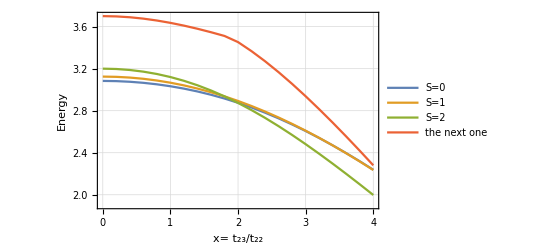

```mathematica
ListLinePlot[{e0data[[1;;21,1;;2]],e1data[[1;;21,1;;2]],e2data[[1;;21,1;;2]],e4data[[1;;21,1;;2]]},PlotLegends->{"S=0","S=1","S=2","the next one"},Frame->True,GridLines->Automatic,AxesLabel->{"x= t_23/t_22","Energy"}]
```

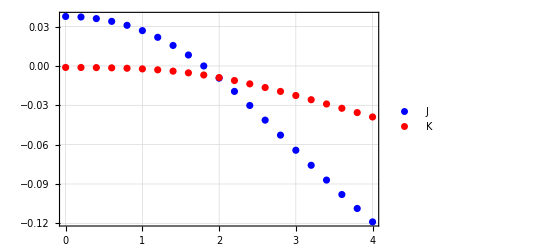

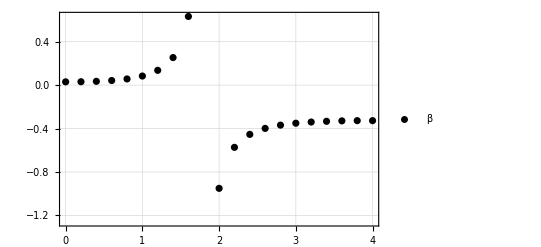

```mathematica
jj1=Table[{e2data[[i,1]],(e2data[[i,2]]-e1data[[i,2]])/2},{i,1,Dimensions[e1data][[1]]}];
jj2=Table[{e2data[[i,1]],e0data[[i,2]]/3.0+e2data[[i,2]]/6.0-e1data[[i,2]]/2.0},{i,1,Dimensions[e1data][[1]]}];
beta=Table[{e2data[[i,1]],-jj2[[i,2]]/jj1[[i,2]]},{i,1,Dimensions[jj1][[1]]}];
ListPlot[{jj1,jj2},PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"J","K"},{Left,Center}],PlotStyle->{Blue,Red}]
ListPlot[beta,PlotRange->Automatic,Frame->True,GridLines->Automatic,PlotLegends->Placed[{"β"},{Left,Center}],PlotStyle->Black]
```